# Mean-Variance Optimization (MVO)

Investing carries with it risk. Given a portfolio of assets, Mean-Variance Optimization aims to allocate your investments between them such that the risk, represented by variance & standard deviation, is minimized for a given expected return.

## Exploration by example

Lets explore the concept of optimal asset allocation by looking at an example portfolio.

### Initialization

Lets select assets from the top 10 performing ETF’s of 2017.

Make a list of assets:

```mathematica
portfolio={"OIH","MUB","PSI","GDX","KRE","ITA","TLT"}
```

{OIH,MUB,PSI,GDX,KRE,ITA,TLT}

For illustrating each asset, we can visualize their corresponding time series.

Get pricing data by specifying 01/01/2010 & 12/31/2016 as a starting and ending dates:

```mathematica
data=FinancialData[#,"Close",{{2010,1,1},{2016,12,31}}]&/@portfolio;
```

Plot combined time series:

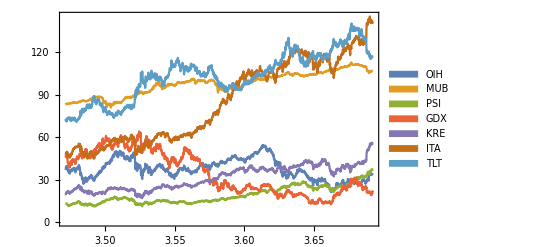

```mathematica
DateListPlot[data,PlotRange->All,Joined->True,PlotLegends->SwatchLegend[portfolio]]
```

In MVO we are interested in returns, that is, the percentage change of each asset’s price with respect to the previous trading day.

Get returns for each asset in portfolio:

```mathematica
returns=FinancialData[#,"FractionalChange",{{2010,1,1},{2016,12,31}},"Value"]&/@portfolio;
```

Plot combined series:

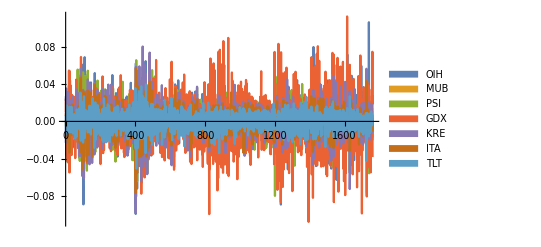

```mathematica
ListPlot[returns,PlotRange->All,Joined->True,PlotLegends->SwatchLegend[portfolio]]
```

### Theory

To perform the optimization, we have to define the necessary quantities first.

#### Weights

Each asset’s allocation is represented by a percentage (weight). Finding the optimal set of weights is the central problem in MVO.

Define unknown weights as a symbolic column vector:

```mathematica
weights=Transpose[{Subscript[w,#]&/@portfolio}];
weights//MatrixForm
```

(w_OIH
w_MUB
w_PSI
w_GDX
w_KRE
w_ITA
w_TLT)

#### Mean Returns

The expected return of our portfolio is given by R = ∑ m · w, where m is a row vector whose entries are given by the mean of each asset’s returns.

Compute the mean for each asset’s returns:

```mathematica
meanRet={Mean[#]&/@returns};
meanRet//MatrixForm
```

(0.000127873 | 0.000146856 | 0.000698028 | -0.000124305 | 0.000698972 | 0.000679286 | 0.000325545)

Compute the annualized portfolio expected return:

```mathematica
portfolioMean=Flatten[meanRet.weights][[1]]*252
```

252 (-0.000124305 w_GDX+0.000679286 w_ITA+0.000698972 w_KRE+0.000146856 w_MUB+0.000127873 w_OIH+0.000698028 w_PSI+0.000325545 w_TLT)

#### Variance

The variance of our portfolio is given by Var = w^T·C· w, where C is the covariance matrix of the returns.

Compute the covariance matrix of our returns:

```mathematica
covMat=Covariance[Transpose[returns]];
covMat//MatrixForm
```

(0.000362878 | -5.28309×10^-6 | 0.000173304 | 0.00015903 | 0.000176886 | 0.000138872 | -0.0000755968
-5.28309×10^-6 | 8.34291×10^-6 | -3.28511×10^-6 | 5.46377×10^-6 | -6.08399×10^-6 | -2.13039×10^-6 | 0.0000101536
0.000173304 | -3.28511×10^-6 | 0.000245512 | 0.0000664025 | 0.000155041 | 0.000131577 | -0.000062709
0.00015903 | 5.46377×10^-6 | 0.0000664025 | 0.000633729 | 0.0000273583 | 0.0000508712 | 0.0000117595
0.000176886 | -6.08399×10^-6 | 0.000155041 | 0.0000273583 | 0.000242485 | 0.000134802 | -0.0000790738
0.000138872 | -2.13039×10^-6 | 0.000131577 | 0.0000508712 | 0.000134802 | 0.000132561 | -0.0000517665
-0.0000755968 | 0.0000101536 | -0.000062709 | 0.0000117595 | -0.0000790738 | -0.0000517665 | 0.0000888442)

Calculate annualized portfolio variance:

```mathematica
portfolioVar=Flatten[Transpose[weights].covMat.weights][[1]]*252;
```

#### Constraints

Constraints are important in making sense out of the optimization process. There are four basic constraints which can be imposed:

∑_i w_i=1

w_i ≥ w_min

w_i ≤ w_max

R_exp ≥ R_min

This function returns a symbolic list of constraints, in terms of asset weights:

```mathematica
constraints[wl_,wg_,retMin_]:=Union[
GreaterEqualThan[wl][#]&/@Flatten[Transpose[weights]],
LessEqualThan[wg][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],
List[GreaterEqualThan[retMin][portfolioMean]]
];
```

Lets impose some basic constraints.

Define the constraints w_i ≥ 0, w_i ≤ 1 & R_exp ≥ 0:

```mathematica
wMin=0.0;
wMax=1;
rMin=0.0;
cons=constraints[wMin,wMax,rMin]
```

{w_GDX+w_ITA+w_KRE+w_MUB+w_OIH+w_PSI+w_TLT==1,w_GDX≥0.,w_ITA≥0.,w_KRE≥0.,w_MUB≥0.,w_OIH≥0.,w_PSI≥0.,252 (-0.000124305 w_GDX+0.000679286 w_ITA+0.000698972 w_KRE+0.000146856 w_MUB+0.000127873 w_OIH+0.000698028 w_PSI+0.000325545 w_TLT)≥0.,w_TLT≥0.,w_GDX≤1,w_ITA≤1,w_KRE≤1,w_MUB≤1,w_OIH≤1,w_PSI≤1,w_TLT≤1}

### Optimization

The optimization consists of minimizing the portfolio variance for a given expected minimum return.

Calculate minimum variance portfolio:

```mathematica
optPort=NMinimize[{portfolioVar,cons},Flatten[weights]]
```

{0.00184663,{w_OIH→0.00817937,w_MUB→0.862513,w_PSI→0.0043036,w_GDX→-2.19213×10^-9,w_KRE→0.0397574,w_ITA→0.0353553,w_TLT→0.0498915}}

We can combine risk (standard deviation) and expected return as a row vector.

Calculate and join risk and expected return for optimal portfolio:

```mathematica
expRetRisk={Sqrt[optPort[[1]]],portfolioMean /.optPort[[2]]}
```

{0.0429724,0.0500883}

Plot asset allocation:

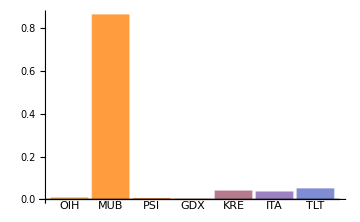

```mathematica
BarChart[{Last[optPort[[2,#]]]&/@Range[Length[portfolio]]},ImageSize->Medium,ChartLabels->portfolio]
```

### Efficient Frontier

The efficient frontier consists in the set of optimal portfolios that offer the lowest level of risk for a given expected return.

Calculate efficient frontier for this example:

```mathematica
effFrontier=Table[{NMinimize[{Sqrt[portfolioVar],Union[GreaterEqualThan[wMin][#]&/@Flatten[Transpose[weights]],
LessEqualThan[wMax][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],List[Equal[portfolioMean,i]]
]
},Flatten[weights]][[1]],i},{i,0.0,1,.001}];//Quiet
```

Plot efficient frontier:

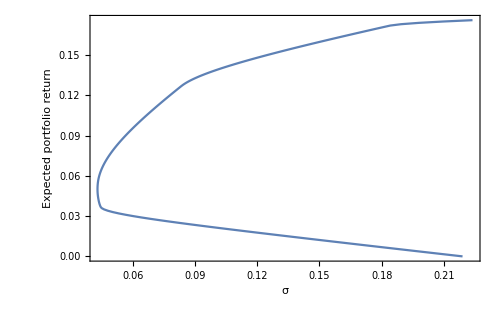

```mathematica
ListLinePlot[
effFrontier,Frame->True,FrameLabel->{"σ","Expected portfolio return"},PlotRange->{Automatic,Automatic},BaseStyle->14,ImageSize->500]
```

Any non optimal portfolio will lie inside the efficient frontier. It is important to note that the “tip” of this graph is our optimal portfolio.

Plot random portfolios along efficient frontier and minimum variance portfolio:

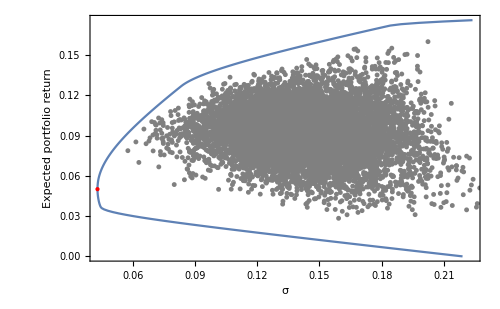

```mathematica
Show[ListLinePlot[effFrontier,Epilog->{Red,PointSize->Large,Point[expRetRisk]},Frame->True,FrameLabel->{"σ","Expected portfolio return"},PlotRange->{Automatic,Automatic},BaseStyle->14,ImageSize->500],ListPlot[
Table[{Sqrt[portfolioVar],portfolioMean}/.Flatten[Select[{Thread[Flatten[Transpose[weights]]->#&[Normalize[RandomReal[{wMin,wMax},Length[portfolio]],Total]]]},AllTrue[#,wMin≤Last[#]≤wMax&]&]],{10000}],
PlotMarkers->{Automatic,5},PlotStyle->Gray]]//Quiet
```

### Performance

If we assume we did this asset allocation from the starting date of our data, we can observe its performance.

Extract asset weights:

```mathematica
alloc=Last[optPort[[2]][[#]]]&/@Range[Length[portfolio]]
```

{0.00817937,0.862513,0.0043036,-2.19213×10^-9,0.0397574,0.0353553,0.0498915}

Weight data based on asset allocations:

```mathematica
port=TimeSeriesThread[alloc.#&,data];
```

Generate a visually appealing graph for optimal portfolio:

```mathematica
pc=PieChart[alloc,ChartLabels->Placed[Style[#,Small,Italic,FontFamily->"Helvetica"]&/@portfolio,"RadialCallout"],ColorFunction->"DarkBands",SectorOrigin->{{π/4,"Clockwise"},0},ChartStyle->Opacity[.6],ImageSize->200,ImagePadding->{{15,15},{0,0}}];
```

Plot portfolio allocation & performance in time:

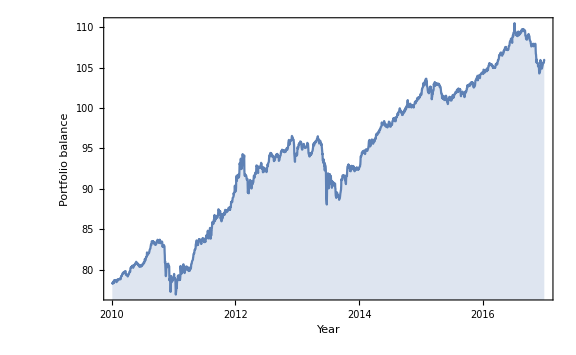

```mathematica
DateListPlot[port,Filling->Axis,Epilog->Inset[pc,{{2011,06,01},103}],ImageSize->Large,FrameLabel->{"Year","Portfolio balance"},BaseStyle->14]
```

This is basically just the performance of asset “MUB”. In the next section we analyze a more realistic example.

## A niftier example

In a more realistic environment, assets weights are restricted to live within a certain range, and portfolio performance is analyzed with future data.

#### Constraints

In this example, lets define weights to be between 5% and 25%.

Generate new constraints:

```mathematica
wMin=0.05;
wMax=0.25;
rMin=0.0;
cons=constraints[wMin,wMax,rMin]
```

{w_GDX+w_ITA+w_KRE+w_MUB+w_OIH+w_PSI+w_TLT==1,w_GDX≥0.05,w_ITA≥0.05,w_KRE≥0.05,w_MUB≥0.05,w_OIH≥0.05,w_PSI≥0.05,252 (-0.000124305 w_GDX+0.000679286 w_ITA+0.000698972 w_KRE+0.000146856 w_MUB+0.000127873 w_OIH+0.000698028 w_PSI+0.000325545 w_TLT)≥0.,w_TLT≥0.05,w_GDX≤0.25,w_ITA≤0.25,w_KRE≤0.25,w_MUB≤0.25,w_OIH≤0.25,w_PSI≤0.25,w_TLT≤0.25}

#### Optimization

Optimizing the portfolio subject to the new constraints leads to interesting changes.

Calculate minimum variance portfolio:

```mathematica
optPort=NMinimize[{portfolioVar,cons},Flatten[weights]]
```

Calculate and join risk and expected return for optimal portfolio:

```mathematica
expRetRisk={Sqrt[optPort[[1]]],portfolioMean /.optPort[[2]]}
```

{0.0829159,0.0990105}

Plot asset allocation:

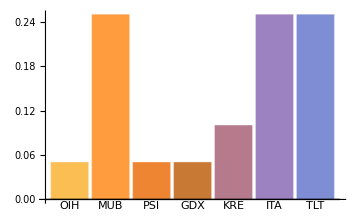

```mathematica
BarChart[{Last[optPort[[2,#]]]&/@Range[Length[portfolio]]},ImageSize->Medium,ChartLabels->portfolio]
```

#### Efficient Frontier

The efficient frontier gets deformed towards a pointy shape.

Calculate efficient frontier for this example:

```mathematica
effFrontier=Table[{NMinimize[{Sqrt[portfolioVar],Union[GreaterEqualThan[wMin][#]&/@Flatten[Transpose[weights]],
LessEqualThan[wMax][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],List[Equal[portfolioMean,i]]
]
},Flatten[weights]][[1]],i},{i,0.0,1,.001}];//Quiet
```

Plot efficient frontier:

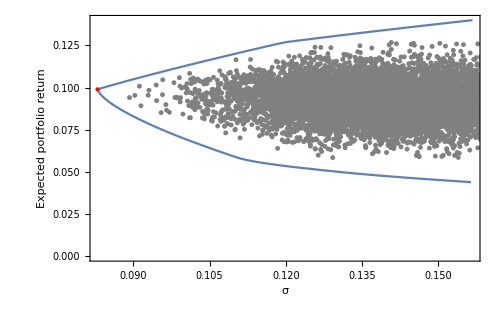

```mathematica
Show[ListLinePlot[effFrontier,Epilog->{Red,PointSize->Large,Point[expRetRisk]},Frame->True,FrameLabel->{"σ","Expected portfolio return"},PlotRange->{Automatic,Automatic},BaseStyle->14,ImageSize->500],ListPlot[
Table[{Sqrt[portfolioVar],portfolioMean}/.Flatten[Select[{Thread[Flatten[Transpose[weights]]->#&[Normalize[RandomReal[{wMin,wMax},Length[portfolio]],Total]]]},AllTrue[#,wMin≤Last[#]≤wMax&]&]],{10000}],
PlotMarkers->{Automatic,5},PlotStyle->Gray]]//Quiet
```

#### Performance

Performance is analyzed by rebalancing portfolios as time progresses.

Extract asset weights:

```mathematica
alloc=Last[optPort[[2]][[#]]]&/@Range[Length[portfolio]]
```

{0.05,0.25,0.0500001,0.05,0.0999999,0.25,0.25}

The following function optimizes a portfolio based on previous information and returns its performance for the next period of time:

```mathematica
backtestShort[startDate_, window_,period_]:=Block[{data,endDate,ret,weights,meanRet,portfolioMean,covMat,portfolioVar,mv,alloc,futureData,port},(
Clear[data,endDate,ret,weights,meanRet,portfolioMean,covMat,portfolioVar,mv,alloc,futureData,port];
endDate=DayPlus[startDate,window*period,"BusinessDay"];
data = FinancialData[#,"Close",{startDate,endDate}]&/@portfolio;
ret=FinancialData[#,"FractionalChange",{startDate,endDate},"Value"]&/@portfolio;
weights=Transpose[{Subscript[w,#]&/@portfolio}];
meanRet={Mean[#]&/@ret};
portfolioMean=Flatten[meanRet.weights][[1]];
covMat=Covariance[Transpose[ret]];
portfolioVar=Flatten[Transpose[weights].covMat.weights][[1]];
mv=NMinimize[{portfolioVar,Union[
GreaterEqualThan[0.05][#]&/@Flatten[Transpose[weights]],
LessEqualThan[0.25][#]&/@Flatten[Transpose[weights]],
List[Total[weights][[1]]==1],
List[GreaterEqualThan[0.0][portfolioMean]]
]},
Flatten[weights]];;
alloc=Last[mv[[2]][[#]]]&/@Range[Length[portfolio]];
futureData= FinancialData[#,"Close",{endDate,DayPlus[endDate,window,"BusinessDay"]}]&/@portfolio;
List[mv[[2]]->TimeSeriesThread[alloc.#&,futureData]]
)];
```

The following generates visually appealing graphs for each period’s portfolio:

```mathematica
portChart[port_]:=Block[{alloc},(
alloc=Last[port[[#]]]&/@Range[Length[portfolio]];
PieChart[alloc,ChartLabels->Placed[Style[#,Small,Italic,FontFamily->"Helvetica"]&/@portfolio,"RadialCallout"],ColorFunction->"DarkBands",SectorOrigin->{{π/4,"Clockwise"},0},ChartStyle->Opacity[.6],ImageSize->150,ImagePadding->{{15,15},{0,0}}]
)];
```

This function loops through periods of time to get joined data:

```mathematica
backtestLong[startDate_,window_,periods_]:=backtestShort[startDate,window,#]&/@Range[periods];
```

We then proceed to initialize with example parameters. Lets say we want 6 periods, each one a year long, beginning at 01/01/2010.

Initializing parameters:

```mathematica
date=DateObject[{2010,1,1}];
wind=252;
period=6;
```

Calculate joined data of the testing in each period:

```mathematica
test=backtestLong[date,wind,period];
```

Plot results:

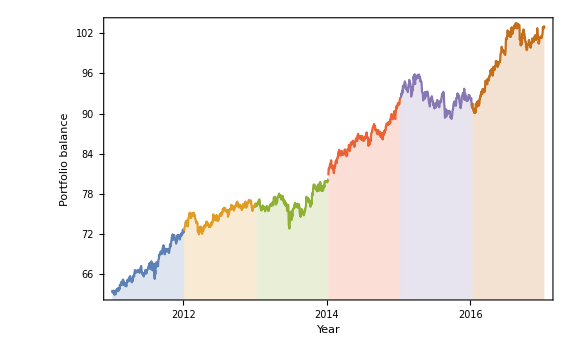

```mathematica
res=Last[test[[#]][[1]]]&/@Range[period];
nf=Nearest[Flatten[bla,1]];
DateListPlot[bla,Filling->Axis,ImageSize->Large,Frame->True,FrameLabel->{"Year","Portfolio balance"},BaseStyle->14,PlotRange->All]//Quiet
```

#### Analysis

Lets take a look at portfolio progression over time, as well as performance per year.

Show portfolio progression through periods:

```mathematica
portfs=First[test[[#]][[1]]]&/@Range[period];
GraphicsGrid[Partition[portChart[portfs[[#]]]&/@Range[period],3],Frame->All]
```

-Graphics-

We see that allocation changes when the optimization gets more data to consider.

Function for getting values from test results for a given year:

```mathematica
yearValues[year_]:=Select[Flatten[res,1],DateValue[First[#],"Year"]==year&];
```

Function to get annual returns out of our data:

```mathematica
returnsByYear[year_]:=(Last[Last[yearValues[year]]]/Last[First[yearValues[year]]])-1;
```

Year list representing time periods:

```mathematica
years={2011,2012,2013,2014,2015,2016};
```

Compute actual annual returns:

```mathematica
annualRet=returnsByYear[#]*100&/@years;
```

Plot returns as bar chart:

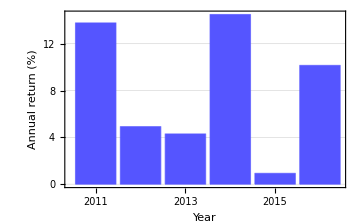

```mathematica
BarChart[{annualRet},ChartStyle-> {Lighter[Blue]},ImageSize->Medium,ChartLabels->years,ImageSize->Small,Frame->True,FrameLabel->{"Year","Annual return (%)"},BaseStyle->14,GridLines->Automatic
]
```

Further Explorations

Compare portfolio performance for different period lengths.

Investigate optimization of parameters such as constraints and number or periods.

Authorship information

Andrés López Martínez

06/20/2017

andoresu@ciencias.unam.mx